```mathematica
latex[x_] := StringReplace[ToString@Format[StandardForm[x],TeXForm], {"<" -> " \lt ", ">" -> " \gt "}]
outputHtml[txt_] := Module[{i,s}, 
	i = Import["D:/GitRoot/llio/web/analysis_aa.stm", "String"];
	s = StringReplace[i, "<!--#include file=\"mathematica.dps_analysis\" -->" -> txt];
	Export["D:/GitRoot/llio/web/analysis_aa.html", s, "String"]
]
```

## AutoAttack DPS

```mathematica
cost /: Subscript[cost, AD] = 36
cost /: Subscript[cost, AS] = 33/Quantity["Percent"]
cost /: Subscript[cost, CC] = 50/Quantity["Percent"]
```

36

33

50

```mathematica
dps /: Subscript[dps, n]  = (Subscript[AD, n] + Subscript[bonus, AD]) * Subscript[AS, n]* (1 + Subscript[bonus, AS]) * (1 + Subscript[bonus, CC])
dps /: Subscript[dps, gold]= Subscript[dps, n] /. {Subscript[bonus, AS] -> Subscript[gold, AS]/Subscript[cost, AS], Subscript[bonus, CC] -> Subscript[gold, CC]/Subscript[cost, CC], Subscript[bonus, AD] -> Subscript[gold, AD]/Subscript[cost, AD]}
```

AS_n (AD_n+bonus_AD) (1+bonus_AS) (1+bonus_CC)

AS_n (AD_n+gold_AD/36) (1+gold_AS/3300) (1+gold_CC/5000)

```mathematica
Clear[g,distro,system,dist]
g = Subscript[dps, gold]{Subscript[gold, AS],Subscript[gold, CC],Subscript[gold, AD]}

systemG = {
	HoldForm[Subscript[dist, CC]'[Subscript[gold, AD]] == (g[[3]]/g[[2]] /. {Subscript[gold, CC] -> Subscript[dist, CC][Subscript[gold, AD]]})],
	HoldForm[Subscript[dist, AS]'[Subscript[gold, AD]] == (g[[3]]/g[[1]] /. {Subscript[gold, AS] -> Subscript[dist, AS][Subscript[gold, AD]]})]
	}
{distribution} = DSolve[ReleaseHold[systemG], {Subscript[dist, CC][Subscript[gold, AD]],Subscript[dist, AS][Subscript[gold, AD]]}, Subscript[gold, AD]]
```

{(AS_n (AD_n+gold_AD/36) (1+gold_CC/5000))/3300,(AS_n (AD_n+gold_AD/36) (1+gold_AS/3300))/5000,1/36 AS_n (1+gold_AS/3300) (1+gold_CC/5000)}

{dist_CC'[gold_AD]==(g⟦3⟧/g⟦2⟧/.{gold_CC→dist_CC[gold_AD]}),dist_AS'[gold_AD]==(g⟦3⟧/g⟦1⟧/.{gold_AS→dist_AS[gold_AD]})}

{{dist_CC[gold_AD]→-5000+C[1] (36 AD_n+gold_AD),dist_AS[gold_AD]→-3300+C[2] (36 AD_n+gold_AD)}}

```mathematica
$Assumptions = {Subscript[AD, n] == 0, Subscript[gold, AD] > 0}
systemAS0 = Flatten[{Subscript[dist, AS][Subscript[gold, AD]] == Subscript[gold, AS], Subscript[gold, AS] == 0,  $Assumptions}] //. Flatten[{distribution,C[1] -> 1,C[2] -> 1}]
resultAS0 = ToRules@Reduce[systemAS0, Reals] (* /. ConditionalExpression[v_,expr_] :> Piecewise[{{v,expr}}] *)

systemCC0 = Flatten[{Subscript[dist, CC][Subscript[gold, AD]] == Subscript[gold, CC], Subscript[gold, CC] == 0, $Assumptions}] //. Flatten[{distribution,C[1] -> 1,C[2] -> 1}]
resultCC0 = ToRules@Reduce[systemCC0, Reals] (* /. ConditionalExpression[v_,expr_] :> Piecewise[{{v,expr}}]  *)

threshold1 = N@(Subscript[gold, AD]/Subscript[cost, AD])/. resultAS0
threshold2 = N@(Subscript[gold, AD]/Subscript[cost, AD])/. resultCC0
```

{AD_n==0,gold_AD>0}

{-3300+36 AD_n+gold_AD==gold_AS,gold_AS==0,AD_n==0,gold_AD>0}

{gold_AD→3300,gold_AS→0,AD_n→0}

{-5000+36 AD_n+gold_AD==gold_CC,gold_CC==0,AD_n==0,gold_AD>0}

{gold_AD→5000,gold_CC→0,AD_n→0}

91.6667

138.889

```mathematica
(* TODO: limits *)
rs = Flatten[{distribution, Subscript[AD, n] -> 0, C[1] -> 1, C[2] -> 1}]
Subscript[dist, CC][Subscript[gold, AD]] //. Flatten[{distribution, Subscript[AD, n] -> 0, Subscript[gold, AD] -> 5000 + 5000, C[1] -> 1}]
Subscript[dist, AS][Subscript[gold, AD]] //. Flatten[{distribution, Subscript[AD, n] -> 0, Subscript[gold, AD] -> 6700 + 3300, C[2] -> 1}]
Subscript[dist, CC][Subscript[gold, AD]] == Subscript[gold, AD] - l2 //. rs
Subscript[dist, AS][Subscript[gold, AD]] == Subscript[gold, AD] - l1 //. rs
```

{dist_CC[gold_AD]→-5000+C[1] (36 AD_n+gold_AD),dist_AS[gold_AD]→-3300+C[2] (36 AD_n+gold_AD),AD_n→0,C[1]→1,C[2]→1}

5000

6700

-5000+gold_AD==-l2+gold_AD

-3300+gold_AD==-l1+gold_AD

```mathematica
l1 = Subscript[gold, AD] /. resultAS0;
l2 = Subscript[gold, AD] /. resultCC0;
gdistroRelAD[ad_] := {ad,Max[0,Subscript[dist, AS][Subscript[gold, AD]]],Max[0,Subscript[dist, CC][Subscript[gold, AD]]]} //. Join[distribution, {Subscript[gold, AD] -> ad, C[1] -> 1, C[2] -> 1, Subscript[AD, n] -> 0}]

Clear[dCC,dAD,dAS,para]
parametricDistroEq = Max[0,Subscript[dist, AS][Subscript[gold, AD]]] + Max[0,Subscript[dist, CC][Subscript[gold, AD]]] + Subscript[gold, AD] == u
goldADofU = Subscript[gold, AD] /. Solve[{Subscript[gold, AD] >= 0, parametricDistroEq} //. rs, Subscript[gold, AD], Reals, MaxExtraConditions->All]
% /. ConditionalExpression[e_,c_] :> 
 	ConditionalExpression[
 	{e, Max[0, Subscript[dist, AS][Subscript[gold, AD]]], Max[0, Subscript[dist, CC][Subscript[gold, AD]]]} //. 
		Append[distribution, Subscript[gold, AD] -> e], c];
% //. {C[1] -> 1, C[2] -> 1};
gdistroset = FullSimplify[%];
conditionalSetToPiecewise[expr_, default_] := Piecewise[expr /. ConditionalExpression[e_,c_] :> {e,c}, default]
gdistro  = conditionalSetToPiecewise[gdistroset, {}]
gdistroD = conditionalSetToPiecewise[D[gdistroset,u], {}]

(*
dAD[h_] := xxx(*&Piecewise[xxx /. ConditionalExpression[e_,c_] :> {e,c}, 0] /. u -> h*)
dCC[h_] := Max[0, Subscript[dist, CC][Subscript[gold, AD]] //. Flatten[{distribution, C[1] -> 1, C[2] -> 1, Subscript[gold, AD] -> dAD[h]}]]
dAS[h_] := Max[0, Subscript[dist, AS][Subscript[gold, AD]] //. Flatten[{distribution, C[1] -> 1, C[2] -> 1, Subscript[gold, AD] -> dAD[h]}]]
*)
(*
para[h_] := {Subscript[gold, AD] -> dAD[h], Subscript[gold, AS] -> dAS[h], Subscript[gold, CC] -> dCC[h]}
paraDPS[h_] := Subscript[dps, gold] /. {Subscript[gold, AD] -> dAD[h], Subscript[gold, AS] -> dAS[h], Subscript[gold, CC] -> dCC[h]}
Plot[{dAD'[h],dAS'[h],dCC'[h]}, {h,0,30000}, PlotRange->{{0,30000},{0,2}}, PlotStyle -> {Directive[Black, Thick], 
				  Directive[Dashed, Red, Thickness[0.015]], 
				  Directive[Blue, Thickness[0.015], Dashing["Large"]],
				  Directive[Green, Thickness[0.015], Dashing["Lage"]]}]
*)
```

Max[0,dist_AS[gold_AD]]+Max[0,dist_CC[gold_AD]]+gold_AD==u

{ConditionalExpression[u,0≤u≤3300],ConditionalExpression[(3300+u)/2,3300<u≤6700],ConditionalExpression[(8300+u)/3,u>6700]}

Piecewise[{{{u,0,0}, 0≤u≤3300}, {{(3300+u)/2,1/2 (-3300+u),0}, 3300<u≤6700}, {{(8300+u)/3,1/3 (-1600+u),1/3 (-6700+u)}, u>6700}, {{}, True}}]

Piecewise[{{{1,0,0}, 0≤u≤3300}, {{1/2,1/2,0}, 3300<u≤6700}, {{1/3,1/3,1/3}, u>6700}, {{}, True}}]

```mathematica
r = 25000;
step = 5000;
(*
data = Flatten[Table[{x,y,z,Subscript[dps, gold]} //. {Subscript[AS, n]->1,Subscript[CC, n]->0,Subscript[AD, n]->50,Subscript[gold, AS]->x,Subscript[gold, CC]->y,Subscript[gold, AD]->z}, {x,0,r,step}, {y,0,r,step}, {z, 0, r, step}], 2];
*)
ascentPath = ParametricPlot3D[gdistro /. {a_,b_,c_} :> {b,c,a} , {u,0,30000}, 
	AxesLabel-> {"Aspd (gold)","Crit (gold)","AD (gold)"},
	PlotStyle->Directive[Thickness[0.0025],RGBColor[16^^FF,0,16^^66,1]], 
	Background->None,
	ViewCenter -> {1/2,1/2,1/2},
	ViewPoint -> {1.4,2,0.4}, 
	ViewVertical->{0.4,0.7,0.9}];

colors[x_] := Blend[{{0, Opacity[1,Darker[Blue]]}, {0.5, Opacity[1,Yellow]}, {1, Opacity[1,Red]}}, x] /.  
	(RGBColor[r_,g_,b_,a_] :> RGBColor[1-r,1-g,1-b,a])

dpsContour = ContourPlot3D[{Subscript[dps, gold]} //. {Subscript[AS, n]->1,Subscript[CC, n]->0,Subscript[AD, n]->50,Subscript[gold, AS]->x,Subscript[gold, CC]->y,Subscript[gold, AD]->z}, {x,0,r},{y,0,r},{z,0,r}, 
	PlotPoints -> 30, MaxRecursion-> 0, Contours -> 150, 
	Mesh -> None,
    Background->None,
	ContourStyle -> Opacity[0.5],
	ColorFunctionScaling  -> True,
	ColorFunction -> Function[{x, y, z, f}, ColorData["BlueGreenYellow"][f]], 
	RegionFunction-> Function[{x,y,z}, x + y + z ≤ r] ];
(*ColorData["AvocadoColors"][f]*)

(*Blend[{{0, Opacity[0.1,Darker[Blue]]}, {800, Opacity[0.2,Yellow]}, {1500, Opacity[0.5,Red]}}, 1000] /. (RGBColor[r_,g_,b_,a_] :> RGBColor[1-r,1-g,1-b,a])*)



thresholdPoints = {0,resultAS0[[1]][[2]],resultCC0[[1]][[2]]}
label[p_,i_] := {
	Graphics3D[Text[ToString[First@i], {-200,-200,800}+p, BaseStyle -> {White, FontSize -> 12, FontFamily -> "Arial"}]],
	Graphics3D[{PointSize[0.008],Red, Point[p]}]
	}

ascentLabeled = Show@@Join[{ascentPath,MapIndexed[label[gdistroRelAD[#1][[{2,3,1}]],#2]&, thresholdPoints]}];
	
(*
dpsGraph = ListPointPlot3D[List /@ data[[All, {1, 2, 3}]], 
 RegionFunction-> Function[{x,y,z}, x + y + z ≤ r],
 PlotStyle -> ({PointSize[Large], 
      colors[#1] } & /@ Flatten[data[[All, {4}]]])];
*)
dpsCombinedGraph = Show[dpsContour,ascentLabeled,
	AxesLabel-> {"Aspd (gold)","Crit (gold)","AD (gold)"},
	Boxed -> True,
	BoxStyle -> Directive[Dotted], 
    Background->None, 
    AxesStyle-> colors[2200] /. (RGBColor[r_,g_,b_,a_] :> RGBColor[r,g,b,1]),
	BoxStyle->White,
	TicksStyle -> White,
	LabelStyle -> Red,

	BaseStyle -> {FontWeight -> "Bold", FontSize -> 14, FontFamily -> "Terminal"},
	BoxRatios->{1,1,0.5},
(*PlotRangePadding -> 0,*)
	ViewCenter -> {1/2,1/2,1/2},
	ImageSize->{500,250},
ViewPoint->{1.7972063735309383,-1.6968044029869762,0.4978340424036346},ViewVertical->{0.6628884964370287,-0.6258227717806889,0.8220090014402306}
]
```

{0,3300,5000}

-Graphics3D-

```mathematica
fileGraphDPS = "images/llio_dps_contour.png"
Export["D:\\GitRoot\\llio\\web\\" <> fileGraphDPS, dpsCombinedGraph, Background -> None, ImageSize->{250*2,250}, BoxRatios->{1,1,1}]
```

images/llio_dps_contour.png

D:\GitRoot\llio\web\images/llio_dps_contour.png

```mathematica
Options[-Graphics3D-]
Options[-Graphics3D-]
```

{Axes→True,AxesLabel→{Aspd (gold),Crit (gold),AD (gold)},AxesStyle→RGBColor[0,NCache[5/9,0.555556],1,1],Background→GrayLevel[0],BaseStyle→{FontWeight→Bold,FontSize→14,FontFamily→Terminal},BoxRatios→{1,1,0.4},BoxStyle→Directive[Dashing[{0,Small}]],Boxed→True,ImageSize→{750.374,254.},LabelStyle→RGBColor[1,0,0],PlotRange→{{0,25000},{0,25000},Automatic},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Automatic,Automatic}},TicksStyle→GrayLevel[1],ViewCenter→{1/2,1/2,1/2},ViewPoint→{1.38042,2.05036,0.102253},ViewVertical→{0.528124,0.791262,0.770506}}

{Axes→True,AxesLabel→{Aspd (gold),Crit (gold),AD (gold)},AxesStyle→RGBColor[0,1,1,1],Background→GrayLevel[0],BaseStyle→{FontWeight→Bold,FontSize→14,FontFamily→Terminal},BoxRatios→{1,1,0.5},BoxStyle→Directive[Dashing[{0,Small}]],Boxed→True,ImageSize→{1500,500},LabelStyle→RGBColor[1,0,0],Lighting→Neutral,Method→{},PlotRange→{{0,25000},{0,25000},{0,25000}},PlotRangePadding→{Scaled[0.02],Scaled[0.02],Scaled[0.02]},TicksStyle→GrayLevel[1],ViewCenter→{1/2,1/2,1/2},ViewPoint→{1.97529,-1.56689,0.00390671},ViewVertical→{0.763848,-0.605122,0.448838}}

```mathematica
costswtf = StringReplace[ToString[{Subscript[cost, AD],Subscript[cost, AS],Subscript[cost, CC]}], "reciprocal percent" -> "/ %"]
html = "</div>
		<div class='analysis_page'>
		<h3> Optimal gold allocation </h3>

		
        <img src='" <> fileGraphDPS <> "'>

		<ul>
		<li> If AD < "<> ToString@threshold1 <>": all gold should be spent to increase AD. </li>
		<li> If " <> ToString@threshold1 <> " < AD < " <> ToString@threshold2 <> ": all gold should be evenly divided between AS and AD. </li>
		<li> If " <> ToString@threshold2 <> " < AD: all gold should be evenly divided between AD/AS/CC until AS and CC reach their hard limits </li>
		</ul>
		Assuming:
		<ul type='square'>
        <li> Gold cost per stat: {AD,AS,CC}=" <> costswtf <> "  </li>
		<li> Critical hit damage bonus: 200% </li>
		</ul>
		
		
		<br>
        </div>

        <div class='analysis_page'>
		<h1> Proof </h1>
		<p>
		Assuming that DPS is calculated as:
        $$ DPS_N = " <> latex[Subscript[dps, n]] <> " $$
        $$AD_n = {base}_{AD} + (n-1) \\cdot {perLV}_{AD}$$
        $$AS_n = {base}_{AS} + (n-1) \\cdot {perLV}_{AS}$$
        $$AD = \\text{attack damage}, AS = \\text{attack speed}, CC = \\text{critical hit chance.}$$
        <br>
        <br>
        Assuming that a unit increase of each stat costs: 
        $$cost_{\\{AD,AS,CC\\}} = " <> latex[{Subscript[cost, AD],Subscript[cost, AS],Subscript[cost, CC]}] <> " $$
        <br>  
        We have dps as a function of gold spent:
        $$DPS_{gold} = " <> latex[Subscript[dps, gold]] <> " $$
        <br>
        Note that the DPS function increases monotonically, so it does not have any extrema.
        </p>
        
        <h3> Optimal gold allocation </h3>
		<p>
       
        Since we are interested in maximizing our DPS per gold spent, i.e. finding the greatest rate of change, 
		and our DPS function is differentiable, the relationship between the input variables and output DPS
		can be found by taking the gradient of the function, using vector calculus.
        $$ g = \\nabla dps_{gold} = \\{dps'_{{gold}_{(gold_{AS})}},dps'_{{gold}_{(gold_{CC})}},dps'_{{gold}_{(gold_{AD})}} \\}$$
        $$ g_1 = " <> latex[g[[1]]] <> " $$
        $$ g_2 = " <> latex[g[[2]]] <> " $$
        $$ g_3 = " <> latex[g[[3]]] <> " $$
        <br>

		Since 'the gradient points in the direction of the greatest rate of increase of the function and its magnitude is the slope of the graph in that direction', 
		the set of points, corresponding to the optimal distributions of gold, is equivalent to the path of steepest ascent on the surface defined by our function. 
		Consequently we find the optimal amount of gold spent on CC and AS, <strong>relative to AD</strong>, by solving the differential system (where /. indicates pattern substitution):
        " <> Fold[#1 <> "$$ " <> latex[#2 //. (Part[g_,i_Integer] :> Subscript[g, i])] <> " $$\n"&, "",systemG] <> "
        yields: 
		$$ " <> latex@distribution[[1]] <> " $$ 
		$$ " <> latex@distribution[[2]] <> " $$ 
		</p>

        <h4>Piecewise intervals</h4>
		<p>
		Clearly, attack speed and crit chance have negative utility when AD levels are low, 
		and since our value of gold spent can't be negative, we need to find the points where they cross zero,
		using them to define seperate intervals.
		<br>
        <br>
		For attack speed we reduce: 
		" <> Fold[#1 <> "$$ " <> latex[#2] <> " $$\n"&, "", systemAS0] <> "
		yielding:
		$$ " <> latex[resultAS0] <> " $$
        <br>

		And for critical hit chance we reduce: 
		" <> Fold[#1 <> "$$ " <> latex[#2] <> " $$\n"&, "", systemCC0] <> "
		yielding:
		$$ " <> latex[resultCC0] <> " $$
        <br>
		Note that we've seen these values before in our algebraic analysis.
		$$ " <> latex[{Subscript[gold, AD]== N@(Subscript[gold, AD]/Subscript[cost, AD])AD /. resultAS0, Subscript[gold, AD] == N@(Subscript[gold, AD]/Subscript[cost, AD]) AD /. resultCC0 }] <> " $$
		</p>

        <h4>Conclusions</h4>
        <p>
		At this point we can draw our initially stated conclusions, simply by looking at the functions, 
		but to further clarify our point we define a new function: 
		$$ f(u)=" <> latex[{Subscript[gold, AD][u],Subscript[dist, AS][Subscript[gold, AD][u]],Subscript[dist, CC][Subscript[gold, AD][u]]}] <> " $$
        <br>
		by solving for gold_AD(u) in:
		$$ " <> latex[parametricDistroEq] <> " $$
		resulting in:
		<br><br>
		$$ gold_{AD}(u)=" <> latex[conditionalSetToPiecewise[goldADofU,0]] <> "$$
        <br><br>
		substituting it back into f(u) yields:
		<br><br>
		$$ f(u)=" <> latex[gdistro] <> "$$
        <br><br>
		taking the first derivative, we see how gold is best divided during each interval:
		<br><br>
		$$ f'(u)=" <> latex[gdistroD] <> "$$
		</p>
	";
(*Fold[#1 <> "gold_{AD}(u)=" <> latex[#2] <> "\\\\"&, "", goldADofU]*)
outputHtml[html]
```

{36, 33 / %, 50 / %}

Part::pspec: Part specification i_Integer is neither a machine-sized integer nor a list of machine-sized integers.

D:/GitRoot/llio/web/analysis_aa.html

## Defensive stat analysis

### Definitions

Incoming damage is classified according to three different types: 
	- TrueDmg (can’t be mitigated)
	- MagicDmg (reduced by magic resist)
	- PhysicalDmg (reduced by armor)
	
Here we define {scaleAR, scaleMR} to be the percentages of total damage consisting of their respective damage types. 
With [scaleAR + scaleMR <= 1.0] and the amount of TrueDmg being implicitly defined by the remainder of [1.0 - (scaleAR + scaleMR) ]

```mathematica
cost /: Subscript[cost, AR] = 20
cost /: Subscript[cost, MR] = 20
cost /: Subscript[cost, HP] = 66/25

ehp /: Subscript[ehp, n] = (Subscript[HP, n]+Subscript[bonus, HP])/(100/(100+Subscript[AR, n]+Subscript[bonus, AR])Subscript[scale, AR] + 100/(100+Subscript[MR, n]+Subscript[bonus, MR])Subscript[scale, MR]+ Subscript[scale, TD])

ehp /: Subscript[ehp, gold] = Subscript[ehp, n] /.{ Subscript[bonus, AR] -> Subscript[gold, AR]/Subscript[cost, AR], 
						Subscript[bonus, MR] -> Subscript[gold, MR]/Subscript[cost, MR], 
						Subscript[bonus, HP] -> Subscript[gold, HP]/Subscript[cost, HP] }

ehpALT = (Subscript[HP, n]+Subscript[bonus, HP])/(100/(100+Subscript[AR, n]+Subscript[bonus, AR]))Subscript[scale, AR] + (Subscript[HP, n]+Subscript[bonus, HP])/(100/(100+Subscript[MR, n]+Subscript[bonus, MR]))Subscript[scale, MR]

ehpALT /. {Subscript[AR, n] -> 0, Subscript[HP, n] -> 0, Subscript[scale, AR] -> 1/4, Subscript[scale, MR] -> 3/4, Subscript[scale, TD] -> 0, Subscript[bonus, MR] -> 0, Subscript[MR, n] -> 0}
Grad[ehpALT /. {Subscript[AR, n] -> 0, Subscript[HP, n] -> 0, Subscript[scale, AR] -> 1/4, Subscript[scale, MR] -> 3/4, Subscript[scale, TD] -> 0, Subscript[bonus, MR] -> 0, Subscript[MR, n] -> 0} , {Subscript[bonus, HP],Subscript[bonus, AR]}]
FullSimplify[%[[2]]/%[[1]]]
ehpALT /. {Subscript[HP, n] -> 2000, Subscript[bonus, HP] -> 0, Subscript[AR, n] -> 100, Subscript[bonus, AR] -> 0, Subscript[scale, AR] -> 1/4, Subscript[scale, MR] -> 3/4, Subscript[scale, TD] -> 0, Subscript[bonus, MR] -> 0, Subscript[MR, n] -> 0 }
```

20

20

66/25

(bonus_HP+HP_n)/((100 scale_AR)/(100+AR_n+bonus_AR)+(100 scale_MR)/(100+bonus_MR+MR_n)+scale_TD)

((25 gold_HP)/66+HP_n)/((100 scale_AR)/(100+AR_n+gold_AR/20)+(100 scale_MR)/(100+gold_MR/20+MR_n)+scale_TD)

1/100 (100+AR_n+bonus_AR) (bonus_HP+HP_n) scale_AR+1/100 (bonus_HP+HP_n) (100+bonus_MR+MR_n) scale_MR

(3 bonus_HP)/4+1/400 (100+bonus_AR) bonus_HP

{3/4+1/400 (100+bonus_AR),bonus_HP/400}

bonus_HP/(400+bonus_AR)

2500

```mathematica
tmpscale = 1
tmpf = Subscript[ehp, gold] /. {Subscript[HP, n] -> 0, Subscript[AR, n] -> 0, Subscript[MR, n] -> 0, Subscript[scale, AR] -> tmpscale, Subscript[scale, MR] -> 1 - tmpscale, Subscript[gold, MR] -> 0, Subscript[scale, TD] -> 0} //. unsub

FullSimplify@Grad[FullSimplify[%], {goldHP,goldAR}];
FullSimplify[%[[2]]/%[[1]]]
% /. {goldAR :> distAR[goldHP]}
DSolve[{distAR'[goldHP] == %}, distAR[goldHP], goldHP];
tmpsol = distAR[goldHP] /. %

"---"
sampleVal = Complex[8000,0]
{maxehp,maxdistro} = FullSimplify@With[{r = {goldHP ≥ 0, goldAR ≥ 0, goldHP + goldAR == sampleVal}},Maximize[{tmpf, r}, {goldHP,goldAR}, Reals]]
N@%


"---"
getC[sol_] := Module[{maxehp,maxdistro,res,hp},
	{maxehp,maxdistro} = With[{r = {goldHP ≥ 0, goldAR ≥ 0, goldHP + goldAR == sampleVal}},Maximize[{tmpf, r}, {goldHP,goldAR}, Reals]];
	hp = (goldHP /. maxdistro);
	res = Reduce[{
		(sol /. goldHP -> hp) == (goldAR /. maxdistro) 
	}, C[1], Complexes];
	res;
	Cases[{res}, Equal[C[1], _], Infinity] /. (Equal[x_,y_] :> y)
]
examine[gld_,{sol_,{}}] := {}
examine[gld_,{{},tmpC_}] := {}
examine[gld_,{sol_,tmpC_}] := Map[Module[{maxehp,maxdistro,res},
	{maxehp,maxdistro} = N@With[{r = {goldHP ≥ 0, goldAR ≥ 0, goldHP + goldAR == gld}},Maximize[{tmpf, r}, {goldHP,goldAR}, Reals]];
	res = N[sol /. {goldHP -> (goldHP /. maxdistro), C[1] -> #}];
	{Append[{Abs[goldHP],Abs[goldAR]}/.maxdistro,"Maximize"],
	{(Abs[goldHP] /. maxdistro), Abs[res], "f"}, C[1] -> #}
]&, tmpC]

tmpsol
tmpC = Map[getC, tmpsol] /. False -> {}
Map[examine[sampleVal,#]&,Thread[{tmpsol,tmpC}]] // TableForm
Map[examine[sampleVal+500,#]&,Thread[{tmpsol,tmpC}]] // TableForm

(*
Reduce[{% == 0,goldHP == 8000/3}, C[1]]
FullSimplify[%]
Solve[% == 0, goldAR]
8000.0/Subscript[cost, HP] *)
```

1

1/264 (100+goldAR/20) goldHP

goldHP/(2000+goldAR)

goldHP/(2000+distAR[goldHP])

{-2000-√(4000000+goldHP^2+2 C[1]),-2000+√(4000000+goldHP^2+2 C[1])}

---

8000

{156250/33,{goldHP→5000,goldAR→3000}}

{4734.85,{goldHP→5000.,goldAR→3000.}}

---

{-2000-√(4000000+goldHP^2+2 C[1]),-2000+√(4000000+goldHP^2+2 C[1])}

{{},{-2000000}}

5000. | 3000. | Maximize
5000. | 3000. | f
C[1]→-2000000 |  |

5250. | 3250. | Maximize
5250. | 3250. | f
C[1]→-2000000 |  |

```mathematica
Cases[goldHP==-2000 (-6+√6)&&C[1]==16000000000/3 (-37+12 √6), C[1]]
LogicalExpand[goldHP==-2000 (-6+√6)&&(y||C[1]==16000000000/3) (-37+12 √6)]

MatchQ[C[1] == (x - 1) (1 + 2 x + 3 x^2), Equal[C[1], _]]
Select[{False,23,False},Not@MatchQ[#,False]&]
"-------"
N@With[{r = goldHP ≥ 0 && goldAR ≥ 0 && goldHP + goldAR == 8000},FindMaximum[{tmpf, r}, {goldHP,goldAR}, Gradient -> Grad[tmpf,{goldHP,goldAD}]]]
Plot3D[(1000 h)/((2000 + a) (3000 + a)),{h,0,8000},{a,0,8000}]
```

{}

goldHP==-2000 (-6+√6)&&(-37+12 √6) (y||C[1]==16000000000/3)

True

{23}

-------

{3049.29,{goldHP→7683.38,goldAR→316.625}}

-Graphics3D-

Compare what stat is more effectively increases the champion’s survival. When m_dmg is increased by health points only bonus_(AR/MR)  == 0.

```mathematica
$Assumptions = {};
ehp /: Subscript[ehp, Subscript[n, HP]]= FullSimplify[Subscript[ehp, n] /. {Subscript[bonus, AR] -> 0, Subscript[bonus, MR] -> 0}]
ehp /: Subscript[ehp, Subscript[n, AR]]= FullSimplify[Subscript[ehp, n] /. {Subscript[bonus, HP] -> 0, Subscript[bonus, MR] -> 0}]
ehp /: Subscript[ehp, Subscript[n, MR]]= FullSimplify[Subscript[ehp, n] /. {Subscript[bonus, HP] -> 0, Subscript[bonus, AR] -> 0}]
```

(bonus_HP+HP_n)/(1-(AR_n scale_AR)/(100+AR_n)-(MR_n scale_MR)/(100+MR_n))

HP_n/(1+(-1+100/(100+AR_n+bonus_AR)) scale_AR-(MR_n scale_MR)/(100+MR_n))

HP_n/(1-(AR_n scale_AR)/(100+AR_n)+(-1+100/(100+bonus_MR+MR_n)) scale_MR)

Assume the same amount of gold spent: hpGold = armGold = mrGold.
To simplify things we collapse scaleAR, scaleMR into one variable, ignoring TrueDamage.

```mathematica
patterns =  {
							 Subscript[bonus, AR] -> Subscript[gold, AR]/Subscript[cost, AR], 
							 Subscript[bonus, MR] -> Subscript[gold, MR]/Subscript[cost, MR], 
							 Subscript[bonus, HP] -> Subscript[gold, HP]/Subscript[cost, HP]}

preferHPoverAR = FullSimplify[(Subscript[ehp, Subscript[n, HP]] == Subscript[ehp, Subscript[n, AR]]) /. patterns]
preferHPoverMR = FullSimplify[(Subscript[ehp, Subscript[n, HP]] == Subscript[ehp, Subscript[n, MR]]) /. patterns]
assumeScaleAR = 3/4
assumeScaleMR = 1/4
$Assumptions = {Subscript[AR, n]≥0,Subscript[MR, n]≥0,Subscript[HP, n]>0,u > 0};
"HP==AR"
{{preferHPoverARcondition}} = Expand@Refine@Solve[{preferHPoverAR, u ≥ 0} //. {Subscript[scale, AR] -> assumeScaleAR, Subscript[scale, MR] -> assumeScaleMR, Subscript[scale, TD] -> 0, Subscript[AR, n] -> 0, Subscript[MR, n] -> 0, Subscript[gold, AR] -> u, Subscript[gold, HP] -> u}, Subscript[HP, n], Reals] 
Expand@FullSimplify[(Subscript[HP, n] Subscript[cost, HP]) //. {preferHPoverARcondition}]
"HP==MR"
{{preferHPoverMRcondition}} = Expand@Refine@Solve[{preferHPoverMR, u ≥ 0} //. {Subscript[scale, AR] -> assumeScaleAR, Subscript[scale, MR] -> assumeScaleMR, Subscript[scale, TD] -> 0, Subscript[AR, n] -> 0, Subscript[MR, n] -> 0, Subscript[gold, MR] -> u, Subscript[gold, HP] -> u}, Subscript[HP, n], Reals] 
Expand@FullSimplify[(Subscript[HP, n] Subscript[cost, HP]) //. {preferHPoverMRcondition}]

$Assumptions = {};
thresholdAR = 3000
thresholdMR = 6000
```

{bonus_AR→gold_AR/20,bonus_MR→gold_MR/20,bonus_HP→(25 gold_HP)/66}

((25 gold_HP)/66+HP_n)/(1-(AR_n scale_AR)/(100+AR_n)-(MR_n scale_MR)/(100+MR_n))==HP_n/(1+(-1+2000/(2000+20 AR_n+gold_AR)) scale_AR-(MR_n scale_MR)/(100+MR_n))

((25 gold_HP)/66+HP_n)/(1-(AR_n scale_AR)/(100+AR_n)-(MR_n scale_MR)/(100+MR_n))==HP_n/(1-(AR_n scale_AR)/(100+AR_n)+(-1+2000/(2000+gold_MR+20 MR_n)) scale_MR)

3/4

1/4

HP==AR

{{HP_n→100000/99+(25 u)/198}}

8000/3+u/3

HP==MR

{{HP_n→100000/33+(25 u)/22}}

8000+3 u

3000

6000

```mathematica
surface = 10−x^2−2y^2
Grad[%,{x,y}]
DSolve[y'[x] == (%[[2]]/%[[1]] /. y->y[x]),y[x],x]
D[surface,y]/D[surface,x]
Integrate[1/y,y] == Integrate[2 1/x,x] + C[1]
(Exp /@ %) /. Exp[C[1]] -> C[2]
"----------"
```

10-x^2-2 y^2

{-2 x,-4 y}

{{y[x]→x^2 C[1]}}

(2 y)/x

Log[y]==C[1]+2 Log[x]

y==x^2 C[2]

----------

```mathematica
dy/dx == FullSimplify[D[eee  /. {goldMR -> 0,goldHP -> x, goldAR -> y}, y]/D[eee  /. {goldMR -> 0,goldHP -> x, goldAR -> y}, x]]
dx*# &/@ % 
((2000+y) (8000+y)) *#&/@%

Integrate[%[[1]] /. dy -> 1, y] == Integrate[%[[2]] /. dx -> 1, x]
FullSimplify[Sqrt /@ %]
Collect[%,y,Simplify]
#/9000& /@ %
Sqrt /@ %
FullSimplify[#,Assumptions-> x≥ 0]& /@ %
tmpres = %[[2]]
Reduce[{8000/3 == % + C, y == 0}, C, Reals]

inv = InverseFunction[Function[z, FullSimplify[8000/3 + tmpres /. y-> z]]]
N@inv[4500]
N@(tmpres + 8000/3) /. y -> 241.80670691847214
```

dy/dx==(6000 x)/((2000+y) (8000+y))

dy==(6000 dx x)/((2000+y) (8000+y))

dy (2000+y) (8000+y)==6000 dx x

16000000 y+5000 y^2+y^3/3==3000 x^2

9000 x^2==y (48000000+y (15000+y))

9000 x^2==48000000 y+15000 y^2+y^3

x^2==(48000000 y+15000 y^2+y^3)/9000

√(x^2)==(√(48000000 y+15000 y^2+y^3))/(30 √10)

x==(√(y (48000000+y (15000+y))))/(30 √10)

(√(y (48000000+y (15000+y))))/(30 √10)

y==0&&C==8000/3

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Function[z,-5000+(27000000 2^(1/3))/((1458000000000-1296000000 z+243000 z^2+√(-2125764000000000000000000+(1458000000000-1296000000 z+243000 z^2)^2))^(1/3))+((1458000000000-1296000000 z+243000 z^2+√(-2125764000000000000000000+(1458000000000-1296000000 z+243000 z^2)^2))^(1/3))/(3 2^(1/3))]

536.902-3.41061×10^-12 ⅈ

3845.08

```mathematica
rules = {Subscript[scale, AR] -> 3/4, Subscript[scale, MR] -> 1/4, Subscript[scale, TD] -> 0, Subscript[MR, n] -> 0, Subscript[AR, n] -> 0, Subscript[HP, n] -> 0};
unsub = (Subscript[x_,s_] :> Symbol[ToString[x]<>ToString[s]]);
eee = Subscript[ehp, gold] /. rules //. unsub;
sysrep = {Subscript[gold, AR] -> Subscript[dist, AR][Subscript[gold, HP]], Subscript[gold, MR] -> Subscript[dist, MR][Subscript[gold, HP]]} //. unsub;
gehp = Grad[eee /. goldMR -> 0, {goldHP,goldAR}]
(*
	HoldForm[Subscript[dist, AR]'[Subscript[gold, HP]] == Piecewise[{{gehp[[1]]/gehp[[2]],Subscript[gold, HP] ≥ 6000}},0] //. ({Subscript[gold, AR] -> Subscript[dist, AR][Subscript[gold, HP]],Subscript[gold, MR] -> Subscript[dist, MR][Subscript[gold, HP]]} //. unsub)],
	HoldForm[Subscript[dist, MR]'[Subscript[gold, HP]] == Piecewise[{{gehp[[1]]/gehp[[3]],Subscript[gold, HP] ≥ 6000}},0] //. ({Subscript[gold, MR] -> Subscript[dist, MR][Subscript[gold, HP]],Subscript[gold, AR] -> Subscript[dist, AR][Subscript[gold, HP]]} //. unsub)],
*)
{maxehp,maxdistro} = With[{mcs = {Subscript[gold, HP] ≥ 0, Subscript[gold, AR] ≥ 0, Subscript[gold, MR] ≥ 0, Subscript[gold, HP] + Subscript[gold, AR] + Subscript[gold, MR] == 8000}},FullSimplify@Maximize[{mf, mcs}, {Subscript[gold, HP],Subscript[gold, AR],Subscript[gold, MR]}, Reals]];
(*
systemEHPG = {
	HoldForm[Subscript[dist, AR]'[Subscript[gold, HP]] == gehp[[2]]/gehp[[1]] //. ({Subscript[gold, AR] -> Subscript[dist, AR][Subscript[gold, HP]] (*,Subscript[gold, MR] -> Subscript[dist, MR][Subscript[gold, HP]]*)} //. unsub)],
	(*HoldForm[Subscript[dist, MR]'[Subscript[gold, HP]] == gehp[[1]]/gehp[[3]] //. ({Subscript[gold, MR] -> Subscript[dist, MR][Subscript[gold, HP]],Subscript[gold, AR] -> Subscript[dist, AR][Subscript[gold, HP]]} //. unsub)], *)
	HoldForm[Subscript[dist, AR][8000/3] == 0]
	(*HoldForm[Subscript[dist, MR][6000] == 0] *)
	} 

(*FullSimplify[ReleaseHold@systemEHPG]*)
FullSimplify[ReleaseHold[systemEHPG] //. unsub]
{distributionEHP} = DSolve[FullSimplify[ReleaseHold[systemEHPG] //. unsub], {distAR[goldHP](*,distMR[goldHP]*)}, goldHP]
FullSimplify[%]

N[{eee /. {goldMR -> 0, goldAR -> distAR[goldHP]}, goldHP,distAR[goldHP],distMR[goldHP]} //. distributionEHP /. goldHP -> 4500]
N[{eee /. {goldMR -> 0, goldAR -> distAR[goldHP]}, goldHP,distAR[goldHP],distMR[goldHP]} //. distributionEHP /. goldHP -> 3000]*)
```

{25/(66 (1/4+75/(100+goldAR/20))),(125 goldHP)/(88 (1/4+75/(100+goldAR/20))^2 (100+goldAR/20)^2)}

```mathematica
(*
distributionEHPN = NDSolve[ReleaseHold[systemEHPG] //. unsub, {distAR[goldHP],distMR[goldHP]}, {goldHP,4000,25000}]
(distMR[goldHP] /. distributionEHPN /. goldHP -> 5000)
(distAR[goldHP] /. distributionEHPN /. goldHP -> 5000)*)
(*
distributionEHPSys = FullSimplify[distributionEHP /. ((a_[b_] -> c_) :> Symbol[ToString[a]<>ToString[b]] == c)] //. {distARgoldHP -> goldAR, distMRgoldHP -> goldMR}
Reduce[Flatten[{distributionEHPSys, goldMR ≥ 0, goldAR ≥ 0}], {goldAR,goldMR}, Reals, Backsubstitution -> True]
{gARMR} = FullSimplify@Solve[Flatten[{distributionEHPSys, goldMR ≥ 0, goldAR ≥ 0}], {goldAR,goldMR}, Reals, MaxExtraConditions -> All]
distDefHP = {goldHP,goldAR,goldMR} /. gARMR 
distDefHP /. goldHP -> 6001
*)
N@With[{mcs = {Subscript[gold, HP] ≥ 0, Subscript[gold, AR] ≥ 0, Subscript[gold, MR] == 0, Subscript[gold, HP] + Subscript[gold, AR] + Subscript[gold, MR] == 3321.22968911227804}},FullSimplify@Maximize[{mf, mcs}, {Subscript[gold, HP],Subscript[gold, AR],Subscript[gold, MR]}, Reals]]
With[{mcs = {Subscript[gold, HP] ≥ 0, Subscript[gold, AR] ≥ 0, Subscript[gold, HP] + Subscript[gold, AR] == (6333)}},NMaximize[{mf /. Subscript[gold, MR] -> 0, mcs}, {Subscript[gold, HP],Subscript[gold, AR]}]]
```

{1269.12,{gold_HP→3079.42,gold_AR→241.807,gold_MR→0.}}

{2706.03,{gold_HP→5059.49,gold_AR→1273.51}}

(25 gold_HP)/(66 (75/(100+gold_AR/20)+25/(100+gold_MR/20)))

-(1. (-8.×10^10-5.×10^7 goldAR-5000. goldAR^2+2000. (4.8×10^7+30000. goldAR+3. goldAR^2)^(2000./(2000.+goldAR)+goldAR/(2000.+goldAR))))/(-3.×10^7-15000. goldAR+(4.8×10^7+30000. goldAR+3. goldAR^2)^(2000./(2000.+goldAR)+goldAR/(2000.+goldAR)))

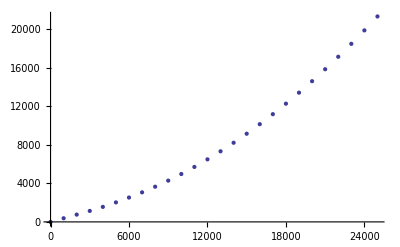

-Graphics3D-

```mathematica
mf = Subscript[ehp, gold] /. rules
(*{3509.445175646108,{Subscript[gold, HP]->5999.999999999994,Subscript[gold, AR]->1514.7186257614296,Subscript[gold, MR]->485.28137423857027}}*)
samples = Table[With[{mcs = {Subscript[gold, HP] ≥ 0, Subscript[gold, AR] ≥ 0, Subscript[gold, MR] ≥ 0, Subscript[gold, HP] + Subscript[gold, AR] + Subscript[gold, MR] == (1000 * u)}},{FullSimplify@Maximize[{mf, mcs}, {Subscript[gold, HP],Subscript[gold, AR],Subscript[gold, MR]}, Reals],u*1000}], {u,0,r/1000}];
N@(distMR[goldHP] /. distributionEHP /. goldHP -> 5000)
(*{Subscript[gold, HP],Subscript[gold, AR],Subscript[gold, MR]} /. samples[[All,1]][[All,2]]*)

Thread[{samples[[All,2]],samples[[All,1]][[All,1]]}];
ListPlot[%]
ps = {Subscript[gold, HP],Subscript[gold, AR],Subscript[gold, MR]} /. N@samples[[All,1]][[All,2]];
maxline = Show[ListPointPlot3D[ps], Graphics3D[ {Red, Line[ps]}, Axes -> True, BoxRatios -> Automatic]]
```

```mathematica
samples2 = Table[With[{mcs = {Subscript[gold, HP] ≥ 0, Subscript[gold, AR] ≥ 0, Subscript[gold, MR] ≥ 0, Subscript[gold, HP] + Subscript[gold, AR] + Subscript[gold, MR] == (1000 * u)}},{FullSimplify@Maximize[{mf, mcs}, {Subscript[gold, HP],Subscript[gold, AR],Subscript[gold, MR]}, Reals],u*1000}], {u,6000/1000,r/1000}];
FindFit[Map[{Subscript[gold, HP],Subscript[gold, AR]} /. #&, samples2[[All,1]][[All,2]]], -6000 + (u b), {a,b}, u]
(*fitA = FindFit[Map[{Subscript[gold, HP],Subscript[gold, AR]} /. #&, samples2[[All,1]][[All,2]]], a + (u b), {a,b}, u]
fitB = FindFit[Map[{Subscript[gold, HP],Subscript[gold, MR]} /. #&, samples2[[All,1]][[All,2]]], a + (u b), {a,b}, u]*)
fitA = Fit[N[Map[{Subscript[gold, HP],Subscript[gold, AR]} /. #&, samples2[[All,1]][[All,2]]], 32], {1,u}, u]
fitB = Fit[N[Map[{Subscript[gold, HP],Subscript[gold, MR]} /. #&, samples2[[All,1]][[All,2]]], 32], {1,u}, u]

Show[maxline,ParametricPlot3D[{u,fitA,fitB}, {u,0,25000}]]
```

{a→0.,b→1.01145}

-1966.52693905099669327637221068+0.631051705221085482256457851642 u

-1922.88870843326139383736196289+0.359291992100451778095522266951 u

-Graphics3D-

```mathematica
ehpContour = ContourPlot3D[{mf} //. {Subscript[gold, HP]->x,Subscript[gold, AR]->y,Subscript[gold, MR]->z}, {x,0,r},{y,0,r},{z,0,r}, 
	PlotPoints -> 15, MaxRecursion-> 0, Contours -> 50, 
	Mesh -> None,
    Background->None,
	ContourStyle -> Opacity[0.5],
	ColorFunctionScaling  -> True,
	AxesLabel-> {Subscript[gold, HP], Subscript[gold, AR] , Subscript[gold, MR]},
	ColorFunction -> Function[{x, y, z, f}, ColorData["BlueGreenYellow"][f]], 
	RegionFunction-> Function[{x,y,z}, x + y + z ≤ r] ]
```

-Graphics3D-

```mathematica
{Subscript[ehp, gold] /. rules} //. {Subscript[gold, HP]->x,Subscript[gold, AR]->y,Subscript[gold, MR]->z}
ehpVector = VectorPlot3D[Grad[Subscript[ehp, gold] /. rules ,{Subscript[gold, HP],Subscript[gold, AR],Subscript[gold, MR]}]//. {Subscript[gold, HP]->x,Subscript[gold, AR]->y,Subscript[gold, MR]->z}, {x,0,r},{y,0,r},{z,0,r}, AxesLabel-> {Subscript[gold, HP], Subscript[gold, AR] , Subscript[gold, MR]}, RegionFunction-> Function[{x,y,z}, x + y + z < r]] (*VectorPoints-> Coarse*)
```

{(25 x)/(66 (200/(3 (100+y/20))+100/(3 (100+z/20))))}

-Graphics3D-

```mathematica
Show[ehpContour, ehpVector, maxline]
```

-Graphics3D-

```mathematica
N@mf /. {Subscript[gold, HP] -> 6000+2 u, Subscript[gold, AR] -> u/2, Subscript[gold, MR] -> u} /. u -> 1500
6000+2 u - 3000+u/2
N@FullSimplify@Solve[{(6000+2 u) + u/2 + u == 9000}, u]
{x,y} //.% /. u -> 9000
ehpContour
```

5250.

3000+(5 u)/2

{{u→857.143}}

{{x,y}}

```mathematica
Grad[(25 h)/(66 (50/(100 + a/20) + 50/(100 + m/20))),{h,a,m}]
```

{25/(66 (50/(100+a/20)+50/(100+m/20))),(125 h)/(132 (100+a/20)^2 (50/(100+a/20)+50/(100+m/20))^2),(125 h)/(132 (50/(100+a/20)+50/(100+m/20))^2 (100+m/20)^2)}